2.30093×10^-8

Power::infy: Infinite expression 1/0. encountered.

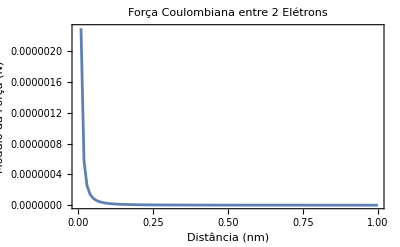

```mathematica
(* Dados 2 elétrons,cada um com carga elétrica−1,60×10−19C,separados por uma distância d=0,1nm,obtenha as forças Coulombianas entre eles,diagramando-as vetorialmente.Use notação vetorial em toda a resolução e faça analiticamente,substituindo numericamente somente ao final. *)

(*Definindo as constantes*)
k=8.988*10^9; (*Constante eletrostática*)
q=1.60*10^-19; (*Carga do elétron em C*)
distanciaEletrons=0.1*10^-9; (*Distância em metros 0.1nm entre os eletrons*)


(*Calcular módulo da força Coulombiana*)
F=(k*q^2)/(distanciaEletrons^2);
F

(*Defina uma função para calcular o módulo da força F(d)*)
Force[d_]:=Abs[(k*q^2)/(d^2)];


(*Criando uma lista de valores de d variando de 0 nm a 1 nm com incremento de 0,01 nm*)
distancias=Range[0,1,0.01]*10^-9;

(*Calculando os valores correspondentes de F(d)*)
forcas=Force/@distancias;

(*Criando o gráfico do módulo da força em função da distância*)
ListLinePlot[Transpose[{distancias*10^9,forcas}],Frame->True,FrameLabel->{"Distância (nm)","Módulo da Força (N)"},PlotLabel->"Força Coulombiana entre 2 Elétrons",AxesLabel->{"d (nm)","F(d) (N)"},PlotRange->All]
```